## Model Setup

```mathematica
wm = ResourceFunction["WolframModel"];
plot = ResourceFunction["WolframModelPlot"];
randomRule = ResourceFunction["RandomWolframModel"];
```

```mathematica
steps=10;
maxValue = 3;
maxVertices=3;
```

```mathematica
randomSignature[maxRelations_, maxElements_, maxPieces_] := 
	Rule @@ Table[
		Table[
			{RandomInteger[{1, maxRelations}], RandomInteger[{1, maxElements}]},
			RandomInteger[{1, maxPieces}]
		], 
		2
	]
```

```mathematica
signature = randomSignature[3, 3, 2]
```

{{3,1}}→{{3,2}}

```mathematica
signature={{2,2}}->{{4,2}}
```

{{2,2}}→{{4,2}}

```mathematica
init = Array[Function[1],signature[[1]][[1]]]
```

{{1,1},{1,1}}

```mathematica
rule=randomRule[signature]
```

{{1,2},{1,3}}→{{1,4},{4,5},{5,2},{3,5}}

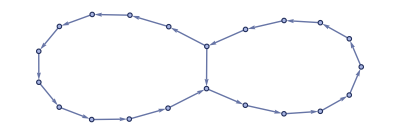

```mathematica
wm[rule, init, steps, "FinalStatePlot"]
```

## Mutations

### Simplest case: retain signature, replace only elements with same range

```mathematica
rule ={rule}
```

{{{1,2},{1,3}}→{{1,4},{4,5},{5,2},{3,5}}}

```mathematica
selectElement[rule_]:=
Module[{replacement, side, edge, vertex, x},
replacement=RandomInteger[{1, Length[rule]}];
x = rule[[replacement]];
side = RandomInteger[{1, 2}];
x = x[[side]];
edge = RandomInteger[{1, Length[x]}];
x = x[[edge]];
vertex = RandomInteger[{1, Length[x]}];
{replacement, side, edge, vertex}
]
```

```mathematica
maxElement[rule_]:=Max[Flatten[List@@@rule]]
```

```mathematica
replaceRandomElement[rule_]:=
ReplacePart[rule, selectElement[rule]->RandomInteger[{1,maxElement[rule]}]]
```

```mathematica
rule
```

{{{1,2},{1,3}}→{{1,4},{4,5},{5,2},{3,5}}}

```mathematica
newRule=replaceRandomElement[rule]
```

{{{1,2},{1,3}}→{{1,4},{4,5},{5,2},{3,5}}}

```mathematica
evolution = wm[newRule, init, steps]
```

WolframModelEvolutionObject[…]

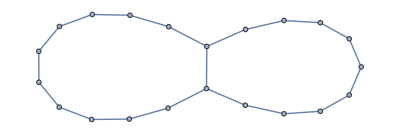

```mathematica
g = Graph@evolution["FinalState"]
```

```mathematica
largestConnectedSubgraph[g_]:=
Subgraph[g, MaximalBy[ConnectedComponents[g], Length]]
```

### Find rules which give connected graphs of increasing dimension

```mathematica
ruleDimension[rule_, nSteps_]:=graphDimension[Graph[wm[rule, {{1,1},{1,1}}, nSteps, "FinalState"]]]
```

```mathematica
graphDimension[graph_] := If[ConnectedGraphQ[graph],
 	ResourceFunction["WolframHausdorffDimension"][graph,All, "AllDimensions","VertexMethod" -> Max],
0]
```

```mathematica
nextGen[rule_,n_,fitnessFunction_]:=
Module[{baseFitness = fitnessFunction[rule], newRules=<||>, newRule, fitness},
While[Length[newRules]<n,
newRule=replaceRandomElement[rule];
If[!KeyExistsQ[newRules, newRule],
fitness = fitnessFunction[newRule];
If[fitness > baseFitness, newRules[newRule] = fitness];
]
];
newRules
]
```

```mathematica
newRules = nextGen[rule,5,Function[rule, -Abs[ruleDimension[rule] -3]]]
```

<|{{{4,2},{3,2}}→{{4,1},{4,2},{5,4},{3,1}}}→-0.235116,{{{1,2},{4,2}}→{{4,1},{4,2},{5,4},{3,1}}}→-0.525861,{{{1,2},{3,2}}→{{4,3},{4,2},{5,4},{3,1}}}→-0.362916,{{{1,2},{3,5}}→{{4,1},{4,2},{5,4},{3,1}}}→-0.257003,{{{1,5},{3,2}}→{{4,1},{4,2},{5,4},{3,1}}}→-0.387945|>

```mathematica
graphRule[rule_]:=wm[rule,{{1,1},{1,1}},7,"FinalStatePlot"]
```

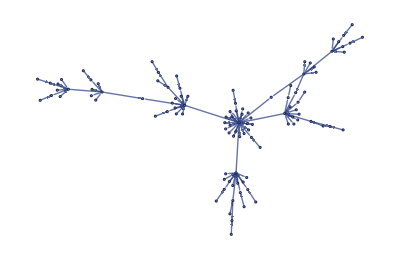
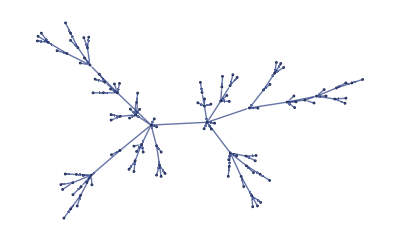
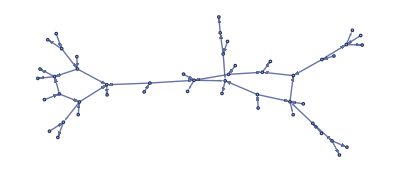
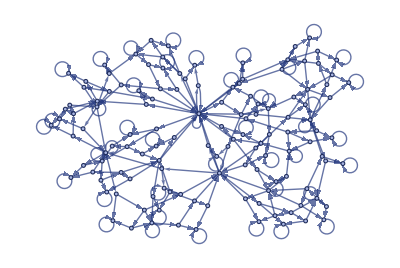
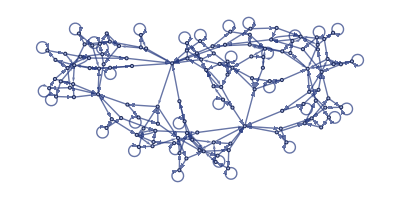

```mathematica
graphRule/@Keys[newRules]
```

```mathematica
evolve[startRule_, fitnessFunction_, nGenerations_] :=
Block[
{rule, fitness},
NestList[CompoundExpression[
rule=replaceRandomElement[First[#]],
fitness=fitnessFunction[rule],
If[fitness >= Last[#], {rule, fitness}, #]
]&, {startRule, fitnessFunction[startRule]}, nGenerations]
]
```

```mathematica
evolution = evolve[rule, -Abs[ruleDimension[#, 7] - 3]&, 20]
```

{{{{{1,2},{1,3}}→{{1,4},{4,5},{5,2},{3,5}}},-1.3555},{{{{1,2},{1,3}}→{{1,4},{4,5},{5,2},{3,5}}},-1.3555},{{{{1,2},{1,3}}→{{1,4},{4,5},{5,2},{3,5}}},-1.3555},{{{{1,2},{1,3}}→{{1,4},{4,5},{5,2},{3,5}}},-1.3555},{{{{1,2},{1,3}}→{{1,4},{4,5},{5,2},{3,5}}},-1.3555},{{{{1,4},{1,3}}→{{1,4},{4,5},{5,2},{3,5}}},-1.19322},{{{{1,4},{1,3}}→{{1,2},{4,5},{5,2},{3,5}}},-0.84058},{{{{1,4},{1,3}}→{{1,2},{4,5},{5,2},{3,5}}},-0.84058},{{{{1,4},{1,3}}→{{1,2},{4,5},{5,2},{3,5}}},-0.84058},{{{{1,4},{1,3}}→{{1,2},{4,5},{4,2},{3,5}}},-0.673155},{{{{1,4},{1,3}}→{{1,2},{4,5},{4,2},{3,5}}},-0.673155},{{{{1,4},{1,3}}→{{1,2},{4,5},{4,2},{3,5}}},-0.673155},{{{{1,4},{1,3}}→{{1,2},{4,5},{4,2},{3,5}}},-0.673155},{{{{1,4},{1,5}}→{{1,2},{4,5},{4,2},{3,5}}},-0.415522},{{{{1,4},{1,2}}→{{1,2},{4,5},{4,2},{3,5}}},-0.183559},{{{{1,4},{1,2}}→{{1,2},{4,5},{4,2},{3,5}}},-0.183559},{{{{1,4},{1,2}}→{{1,2},{4,5},{4,2},{3,5}}},-0.183559},{{{{1,4},{1,2}}→{{1,2},{4,5},{4,2},{3,5}}},-0.183559},{{{{1,4},{1,2}}→{{1,2},{4,5},{4,2},{3,5}}},-0.183559},{{{{1,4},{1,2}}→{{1,2},{4,5},{4,2},{3,5}}},-0.183559},{{{{1,4},{1,2}}→{{1,2},{4,5},{4,2},{3,5}}},-0.183559}}

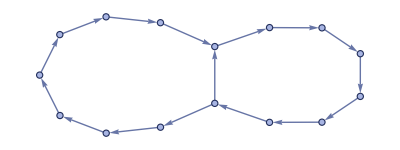
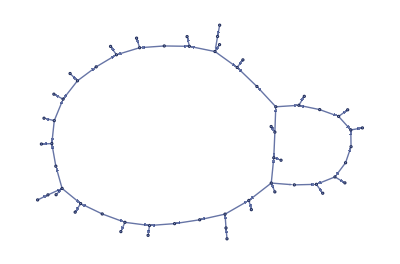
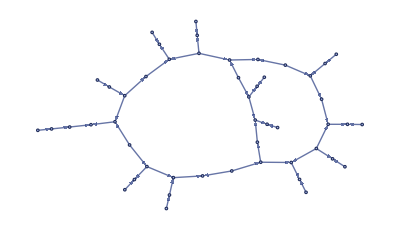
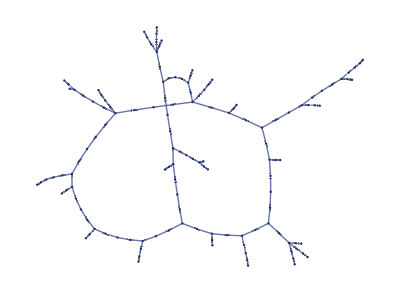
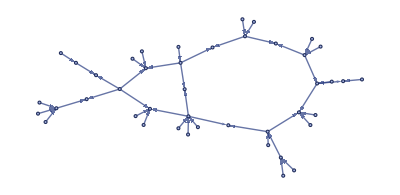
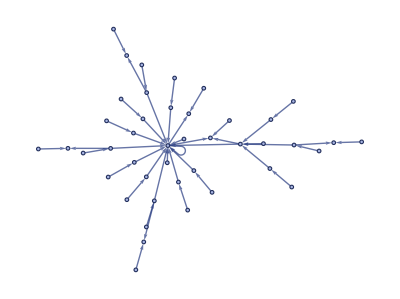
{-Graphics--1.3555,-Graphics--1.3555,-Graphics--1.3555,-Graphics--1.3555,-Graphics--1.3555,-Graphics--1.19322,-Graphics--0.84058,-Graphics--0.84058,-Graphics--0.84058,-Graphics--0.673155,-Graphics--0.673155,-Graphics--0.673155,-Graphics--0.673155,-Graphics--0.415522,-Graphics--0.183559,-Graphics--0.183559,-Graphics--0.183559,-Graphics--0.183559,-Graphics--0.183559,-Graphics--0.183559,-Graphics--0.183559}

```mathematica
Labeled[graphRule[First[#]], Last[#]]&/@evolution
```